```mathematica
Get["Spectra/ElectronSpectrum.m"]
```

Set::wrsym: Symbol pmax is Protected.

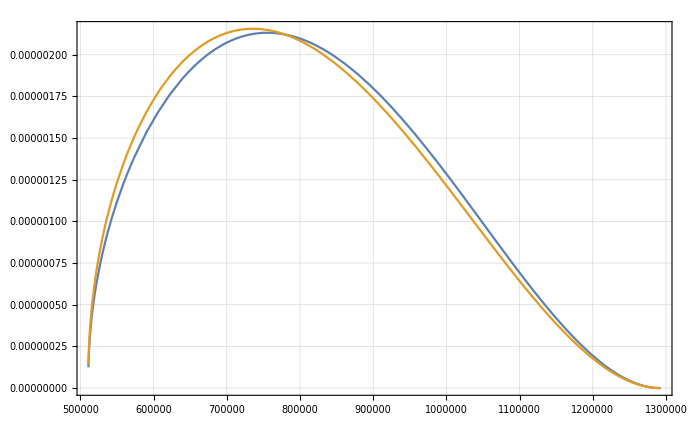

```mathematica
Plot[{
weNormed[λ0,κ0,0.,Ee],
weNormed[λ0,κ0,0.5,Ee]},
{Ee,me,E0}
]
```

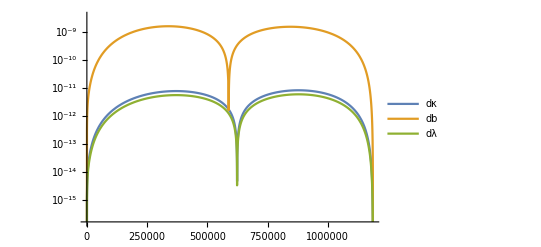

```mathematica
LogPlot[
{
Abs[wmomNormedWb[λ0,κ0,0.,p]-
wmomNormedWb[λ0,κ0*1.01,0.,p]],
Abs[wmomNormedWb[λ0,κ0,0.,p]-
wmomNormedWb[λ0,κ0,0.01,p]],
Abs[(wmomNormedWb[λ0,κ0,0.,p]-
wmomNormedWb[λ0*1.01,κ0,0.,p])]
}
,{p,0,pmax},PlotLegends->{"dκ","db","dλ"}]
```

```mathematica
Manipulate[Plot[(wmomNormedWb[λ0,κ0,0.,p]-
wmomNormedWb[λ0,κ0*0.01,0.,p])-(wmomNormedWb[λ0,κ0,0.,p]-wmomNormedWb[λ0*0.01,κ0,0.,p])*scale,{p,0,pmax},PlotRange->{-2*10^-12,2*10^-12}],{scale,0.63,0.69}]
```

Plot::plln: Limiting value pmax in {p,0,pmax} is not a machine-sized real number.

General::munfl: Exp[-966.245] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-966.245] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-966.245] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-949827.] is too small to represent as a normalized machine number; precision may be lost.

```mathematica
testdata=Table[{Ee,R0[λ0,κ0,Ee]},{Ee,me,E0,(E0-me)/1000}];
```

```mathematica
testfit=NonlinearModelFit[testdata,
R0[l,k,Ee],{l,k},Ee]
```

FittedModel[0.021949 (-44.2596 (0.00275144+555.829/Ee-4.25729×10^-9 Ee)+14.8534 (-0.00275144-555.829/Ee+1.06432×10^-8 Ee)+2.12864×10^-9 Ee)]

```mathematica
testfit["CorrelationMatrix"]
```

{{1.,1.},{1.,1.}}

```mathematica
Manipulate[Plot3D[R0[l,k,Ee],{l,-1.28,-1.26},{k,1.8,1.9}],{Ee,me,E0}]
```

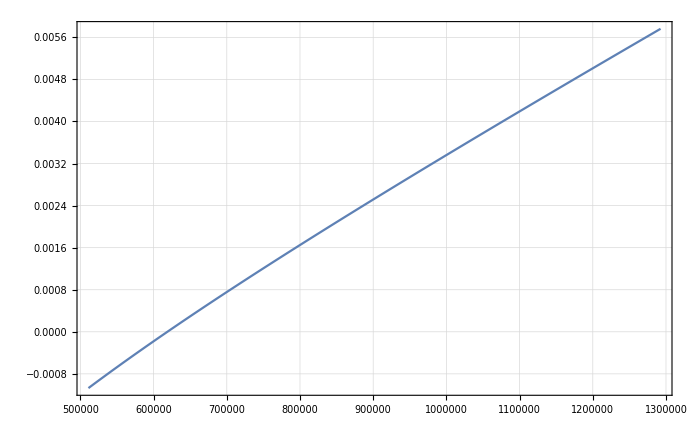

```mathematica
Plot[R0[λ0,κ0,Ee],{Ee,me,E0}]
```

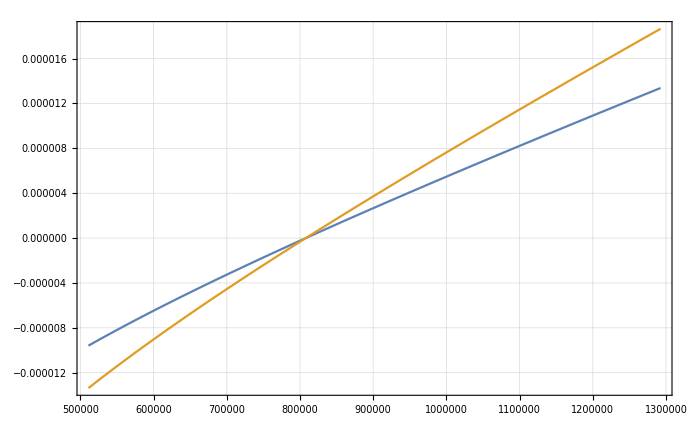

```mathematica
Plot[{
R0[λ0,κ0,Ee]-R0[λ0*1.01,κ0,Ee],
-(R0[λ0,κ0,Ee]-R0[λ0,κ0*1.01,Ee])
},{Ee,me,E0}]
```

### Proton spectrum

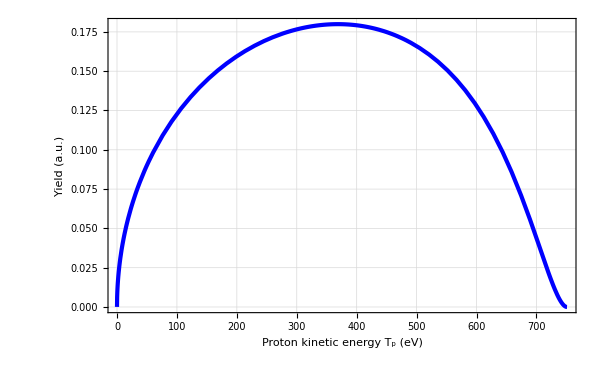

```mathematica
ProtonRawEnergySpectrumPlot=Plot[dwdtNormed[T,-0.103]*100,{T,0,751},LabelStyle->{FontFamily->"Helvetica",25,Black,Bold},FrameLabel->{{"Yield (a.u.)",None},{"Proton kinetic energy T_p (eV)",None}},PlotStyle->Directive[Thickness[0.005],Blue],ImageSize->600]
```

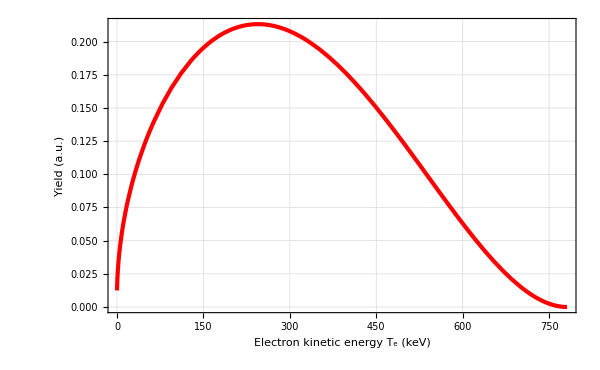

```mathematica
ElectronRawEnergySpectrumPlot=Plot[weNormed[λ0,κ0,0.,T*1000+me]*10^5,{T,0,781},LabelStyle->{FontFamily->"Helvetica",25,Black,Bold},FrameLabel->{{"Yield (a.u.)",None},{"Electron kinetic energy T_e (keV)",None}},PlotStyle->Directive[Thickness[0.005],Red],ImageSize->600]
```

```mathematica
Export["~/Dropbox/PhD/ElectronRawEnergySpectrum.png",ElectronRawEnergySpectrumPlot,ImageResolution->450];
Export["~/Dropbox/PhD/ProtonRawEnergySpectrum.png",ProtonRawEnergySpectrumPlot,ImageResolution->450];
```

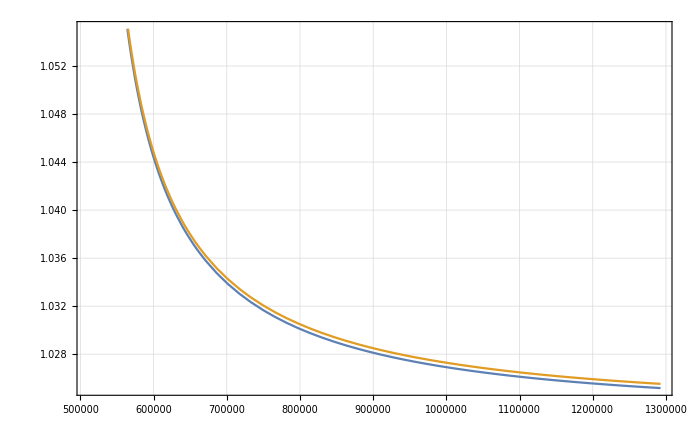

```mathematica
Plot[{F[Ee],Fapprox[Ee]},{Ee,me,E0}]
```

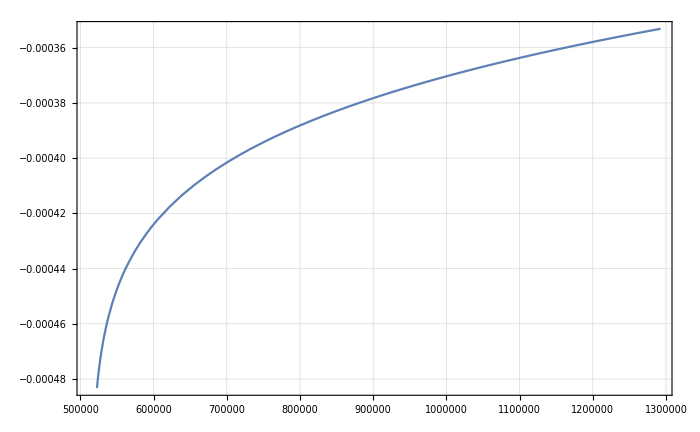

```mathematica
Plot[F[Ee]-Fapprox[Ee],{Ee,me,E0}]
```

General::munfl: Exp[-16227.6] is too small to represent as a normalized machine number; precision may be lost.

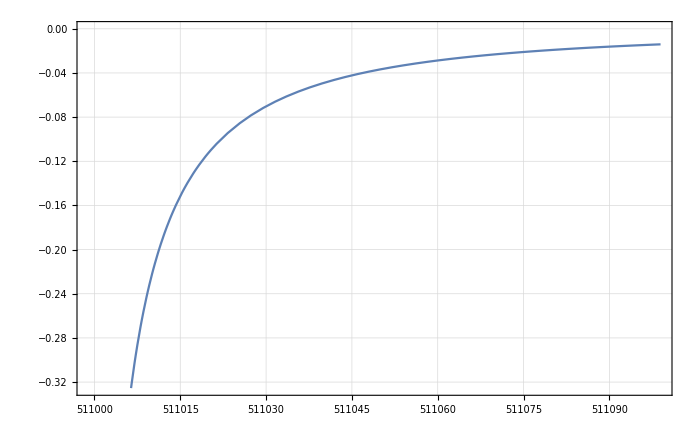

```mathematica
Plot[(F[Ee]-Fapprox[Ee])/F[Ee],{Ee,me,me+100}]
```

```mathematica
F[me+0.01]
```

231.822

```mathematica
FPiecewise[me+0.01]
```

163.923